## First some formulae

```mathematica
FormulaGraphReverse2[allGraphs5[lambdaKey,"colofourgenerator"]]//VertexList
```

{g13x24x5,g13x25x4,g14x25x3,g14x2x35,g1x24x35,g1x2x3x4x5,g13x2x4x5,g14x2x3x5,g1x24x3x5,g1x25x3x4,g1x2x35x4}

```mathematica
FormatCoeff[c_]:=Framed[If[c<0,Style[c,Red,Bold],Style[c,Darker[Green],Italic]], Background->LightYellow]
```

```mathematica
Bases["F","Colofour"]
```

colofournull

```mathematica
Keys[allGraphs5[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
Clear[GenGraph]
```

```mathematica
GenGraph[k_Integer, base_String:"G"]:=Labeled[ShowGraph5Least[k],Style[allGraphs5[k,"embed"],Italic,Red]]->GenGraph[allGraphs5[k,Bases[base,"Colofour"]],base]
```

```mathematica
GenGraph[form_, base_String:"G"]:=With[{g=FormulaGraphReverse2[form]},
Graph[g,VertexLabels->Map[#->Labeled[(#/.RepGraph[base]),FormatCoeff[Coefficient[form,#]]->(#/.RepEmbed[base])]&,VertexList[g]],
ImageSize->400
]
]
```

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull,colofournull,colofourgenerator}

```mathematica
GenGraph6[k_Integer, base_String:"G"]:=ShowGraph6Least[k]->GenGraph6[allGraphs6[k,Bases[base,"Colofour"]],base]
```

```mathematica
GenGraph6[form_, base_String:"G"]:=With[{g=FormulaGraphReverse2[form]},
Graph[g,VertexLabels->Map[#->Labeled[(#/.RepGraph6[base]),FormatCoeff[Coefficient[form,#]]]&,VertexList[g]],
ImageSize->400
]
]
```

## Then some pcitures

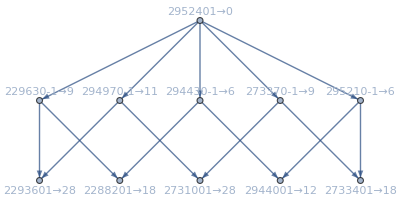
-Graphics-20665363→-Graphics-

```mathematica
GenGraph[lambdaKey]
```

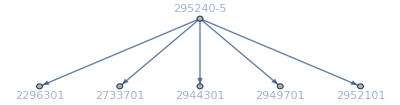

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]]
```

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]==0//Simplify
```

g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35+5 g1x2x3x4x5==2 (g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4)

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]==0//Simplify
```

g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4==5 g1x2x3x4x5

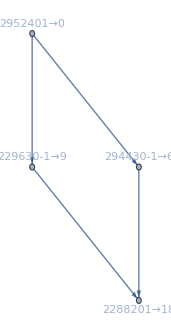
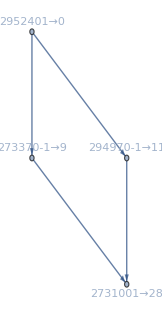
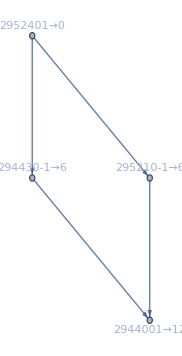
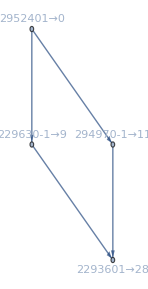
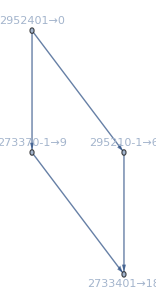
{-Graphics-361660→-Graphics-,-Graphics-317380→-Graphics-,-Graphics-296080→-Graphics-,-Graphics-361120→-Graphics-,-Graphics-317140→-Graphics-}

```mathematica
Table[GenGraph[k],{k,alfa1s}]
```

```mathematica
Table[allGraphs5[k,"colofourgenerator"]/.RepGraph["G"],{k,quads}]
```

{-Graphics-229630--Graphics-295240,-Graphics-294430--Graphics-295240,-Graphics-295210--Graphics-295240,-Graphics-273370--Graphics-295240,-Graphics-294970--Graphics-295240}

```mathematica
Table[GenGraph[k],{k,quads}]
```

{-Graphics-360850→-Graphics-,-Graphics-296050→-Graphics-,-Graphics-295270→-Graphics-,-Graphics-317110→-Graphics-,-Graphics-295510→-Graphics-}

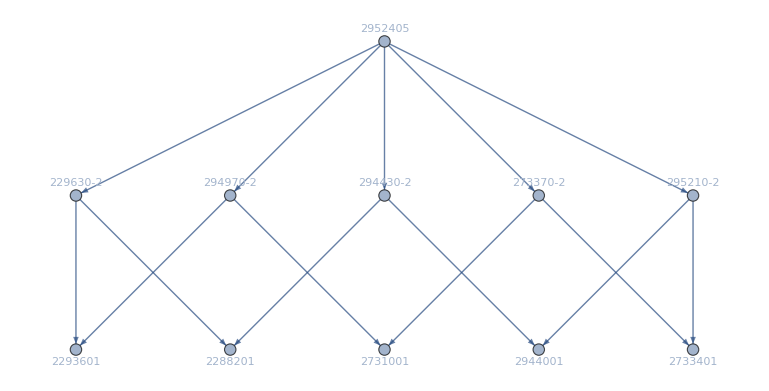

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]]
```

```mathematica
Reduce[(g1x2x3x4x5==0
&&top==g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4
&&bottom==g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]==0)
/.g1x2x3x4x5->0,{g13x24x5,g13x25x4,g13x2x4x5,g14x25x3,g14x2x35,g14x2x3x5,g1x24x35,g1x24x3x5,g1x25x3x4,g1x2x35x4,g1x2x3x4x5},Reals]
```

bottom==2 top&&g1x24x35==-g13x24x5-g13x25x4-g14x25x3-g14x2x35+2 top&&g1x2x35x4==-g13x2x4x5-g14x2x3x5-g1x24x3x5-g1x25x3x4+top

```mathematica
Reduce[(g1x2x3x4x5==0
&&top ==g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4
&&bottom==g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]>0
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfas}]]>0
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,{lambdaKey}}]]>0
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,{starKey}}]]>0)
/.g1x2x3x4x5->0,{g13x24x5,g13x25x4,g13x2x4x5,g14x25x3,g14x2x35,g14x2x3x5,g1x24x35,g1x24x3x5,g1x25x3x4,g1x2x35x4,g1x2x3x4x5},Reals]
```

bottom>0&&0<top<(2 bottom)/3&&g12x34x5>-g12x3x45+g12x3x4x5-g15x23x4-g15x2x34+g15x2x3x4-g1x23x45+g1x23x4x5+g1x2x34x5+g1x2x3x45&&g1x24x35==bottom-g13x24x5-g13x25x4-g14x25x3-g14x2x35&&g1x2x35x4==-g13x2x4x5-g14x2x3x5-g1x24x3x5-g1x25x3x4+top

```mathematica
Assuming[top>0,Sort[{(2 top)/3,top/2}]]
```

{top/2,(2 top)/3}

```mathematica
g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4/.RepGraph["G"]
```

-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630

```mathematica
g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35/.RepGraph["G"]
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820

```mathematica
Reduce[(g1x2x3x4x5==0
&&top==g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4
&&bottom==g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]==0
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]>0
&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfas}]]>0
&&allGraphs5[lambdaKey,"colofourgenerator"]>0)
/.g1x2x3x4x5->0,{g13x24x5,g13x25x4,g13x2x4x5,g14x25x3,g14x2x35,g14x2x3x5,g1x24x35,g1x24x3x5,g1x25x3x4,g1x2x35x4,g1x2x3x4x5},Reals]
```

top>0&&bottom==2 top&&g1x24x35==-g13x24x5-g13x25x4-g14x25x3-g14x2x35+2 top&&g1x2x35x4==-g13x2x4x5-g14x2x3x5-g1x24x3x5-g1x25x3x4+top

```mathematica
ListofVars[top>0&&bottom==top/2&&g1x2x35x4==bottom-g13x2x4x5-g14x2x3x5-g1x24x3x5-g1x25x3x4&&g1x2x3x4x5==0&&g13x24x5==-g13x25x4-g14x25x3-g14x2x35-g1x24x35+top]//Sort
```

{bottom,bottom,g13x24x5,g13x25x4,g13x2x4x5,g14x25x3,g14x2x35,g14x2x3x5,g1x24x35,g1x24x3x5,g1x25x3x4,g1x2x35x4,g1x2x3x4x5,top,top,top}

top is

```mathematica
g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4/.RepEmbed["G"]
```

41

```mathematica
g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4/.RepGraph["G"]
```

-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630

```mathematica
bottom is
```

```mathematica
g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35/.RepEmbed["G"]
```

104

```mathematica
g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35/.RepGraph["G"]
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820

```mathematica
41<2/3*104
```

True

```mathematica
2/3*104-41
```

85/3

```mathematica
0<g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4<2/3(g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35)/.RepGraph["G"]
```

0<-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630<2/3 (-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820)

```mathematica
repFull=Table[allGraphs5[k,"colofourgenerator"]->allGraphs5[k,"colofour"],{k,allGraphs5GeneratorAtomKeys}];
```

```mathematica
repEmpty=Table[allGraphs5[k,"colofourgenerator"]->allGraphs5[k,"colofourrealnull"],{k,allGraphs5GeneratorAtomKeys}];
```

```mathematica
g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4==(g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35)/2/.repFull
```

v13x2x4x5+v14x2x3x5+v1x24x3x5+v1x25x3x4+v1x2x35x4+5 v1x2x3x4x5==1/2 (v13x24x5+v13x25x4+2 v13x2x4x5+v14x25x3+v14x2x35+2 v14x2x3x5+v1x24x35+2 v1x24x3x5+2 v1x25x3x4+2 v1x2x35x4+5 v1x2x3x4x5)

```mathematica
0<g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4<2/3(g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35)/.RepGraph["G"]
```

0<-Graphics-295210+-Graphics-294970+-Graphics-294430+-Graphics-273370+-Graphics-229630<2/3 (-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820)

```mathematica
((g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4==(g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35)/2/.repFull)//Simplify)/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080==5 -Graphics-295240

```mathematica
((g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4==(g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35)/2/.repEmpty)//Simplify)/.RepGraph["E"]
```

110 -Graphics-590481+10 -Graphics-529745+10 -Graphics-439024+5 -Graphics-393845+10 -Graphics-408785+5 -Graphics-393724+5 -Graphics-393685+10 -Graphics-175144+5 -Graphics-48604+10 -Graphics-6665+4 -Graphics-132842+10 -Graphics-145864+5 -Graphics-19445+10 -Graphics-5464+4 -Graphics-131762+5 -Graphics-131244+5 -Graphics-4885+10 -Graphics-58345+5 -Graphics-16204+10 -Graphics-2184+4 -Graphics-44282+5 -Graphics-14765+5 -Graphics-724+10 -Graphics-265+4 -Graphics-43802+4 -Graphics-1682+5 -Graphics-034==29 -Graphics-575282+29 -Graphics-544922+10 -Graphics-529762+29 -Graphics-454162+10 -Graphics-408962+10 -Graphics-393922+8 -Graphics-439081+29 -Graphics-189802+10 -Graphics-63202+10 -Graphics-21242+29 -Graphics-7282+8 -Graphics-49201+8 -Graphics-147481+8 -Graphics-133401+8 -Graphics-175681+5 -Graphics-3936613+5 -Graphics-1312210+5 -Graphics-48613+5 -Graphics-437410+5 -Graphics-16210+5 -Graphics-1813+5 -Graphics-145813+5 -Graphics-5410+5 -Graphics-213+5 -Graphics-610

```mathematica
((0<g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4<2/3(g13x24x5+g13x25x4+g14x25x3+g14x2x35+g1x24x35)/.repFull)//Simplify)/.RepGraph["C"]
```

-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+5 -Graphics-295240>0&&2 -Graphics-361660+2 -Graphics-361120+2 -Graphics-317380+2 -Graphics-317140+2 -Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270>5 -Graphics-295240

```mathematica
Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,"colofourgenerator"]]]==52&]
```

{59048}

```mathematica
Map[Length[ListofVars[allGraphs5[#,"colofourgenerator"]]]&,Keys[allGraphs5]]//Tally//Sort
```

{{1,52},{2,50},{3,290},{4,125},{5,145},{6,30},{7,150},{8,120},{9,210},{10,190},{11,67},{12,60},{13,70},{14,35},{15,35},{16,75},{17,10},{20,20},{21,30},{25,10},{27,30},{31,30},{37,10},{38,10},{48,25},{51,15},{52,1}}

```mathematica
allGraphs5[59048,"graph"]
```

-Graphics-

```mathematica
Length[ListofVars[allGraphs5[0,"colofourgenerator"]]]
```

1